## SED

```mathematica
e:=4.8*10^-10              (*StatCoulomb*)
Bcgs:=7*10^-6                    (*Gauss=cm^(-1/2)g^(1/2)s^-1*)
Bsi:=7*10^-10                    (*Tesla*)   
mc2:=511000                     (*eV*)
m:=9.1*10^-28                     (*g*)
c:=3*10^10                          (*cm/s*)
h:=6.63×10^-27               (*ergios s*)
pc2cm:=3.0857 10^18
Rout:= 10*pc2cm(*cm*)
Rin:= 7.5*pc2cm(*cm*)
Dsrn:=15000*pc2cm
f2L:=4*π*Dsrn^2  (*factor para pasar de flujo a luminosidad en tabla *)
V:=4/3*π*(Rout^3-Rin^3)   (*cm^3*)
fvol:=0.16
α:=1.9
A:=2.36 10^-12  (*en cgs*)
CC:=1.85       (*viene de la aproximacion bessel*)
Eemaxev:=3.176*10^13             (*eV*)
Eeminev:=1*10^6                         (*=Eph/Ec   eV*)
Eemaxerg:=3.176*10^13*1.602*10^-12            (*ergios*)
Eeminerg:=1.61*10^-6                      (*ergios*)
erg2ev:=1/ev2erg
ev2erg:=1.602*10^-12
Ae := 0.0975 (*ev^0.9 cm^-3*)
Eemax:=3.176*10^13 (*eV*)
β:=1/137
re:=2.8179*10^-13  (*cm*)
n:=0.011 (*cm^-3*)
κ:=0.17
Eerep:=511000 (*eV*)
Eemin:=1 10^6 (*eV*)(*1MeV*)
k:=8.61*10^-5;      (*eV/kelvin*)
T:=2.7 (*Kelvin*)
hev:=4.13*10^-15(*eV s*)
σT:=0.66 10^-24 (*cm^2*)
Eprep:=938257 10^3 (*eV*);
Eπrep:= 139600 10^3(*eV*);
Epmax:=2.5553 10^13 (*eV*);
Ap:=42.5397818502(*eV^0.9 cm^-3*);
```

```mathematica
(*Sincro*)
PP[Eph_,Ee_]:=(√3*π*e^3*Bcgs)/(h*m*c^2)*CC*(Eph/(3/(4π)*(e*h*Bcgs)/(m*c)*(Ee/(m*c^2))^2))^(1/3)*ⅇ^(-(Eph/(3/(4π)*(e*h*Bcgs)/(m*c)*(Ee/(m*c^2))^2))) 
NSinc[Ee_]:=A*Ee^-α*ⅇ^(-Ee/Eemaxerg)

P[Eph_]:=NIntegrate[PP[Eph,Ee]*NSinc[Ee],{Ee,Eeminerg,Eemaxerg},AccuracyGoal->12]

L[Eph_]:=Eph*P[Eph]*V*fvol

(*Brems*)
σ[Eγ_,Ee_]:=(4*β*re^2)/Eγ*ϕ[Eγ,Ee]*ev2erg (*cm^2 eV^-1*)
ϕ[Eγ_,Ee_]:=(1+(1-Eγ/Ee)^2-2/3*(1-Eγ/Ee))*Log[191]+1/9*(1-Eγ/Ee)
I1[Ee_]:=c/(4π)*Ae*Ee^-α*ⅇ^(-Ee/Eemax)
(*IC*)
ϵph[Eph_]:=Eph/Eerep
ϵγ[Eγ_]:=Eγ/Eerep
γ[Ee_]:= Ee/Eerep
x[Ee_,Eph_,Eγ_]:= ϵγ[Eγ]/(4ϵph[Eph] γ[Ee]^2(1-ϵγ[Eγ]/γ[Ee]))
P[Ee_,Eph_,Eγ_]:=HeavisideTheta[1-x[Ee,Eph,Eγ]]HeavisideTheta[x[Ee,Eph,Eγ]-1/(4 γ[Ee]^2)]
f[Ee_,Eγ_,Eph_]:= (2x[Ee,Eph,Eγ] Log[x[Ee,Eph,Eγ]]+x[Ee,Eph,Eγ]+1-2 x[Ee,Eph,Eγ]^2+((4ϵph[Eph] γ[Ee] x[Ee,Eph,Eγ])^2(1-x[Ee,Eph,Eγ]))/(2 (1+4 ϵph[Eph] γ[Ee] x[Ee,Eph,Eγ])))P[Ee,Eph,Eγ]
σIC[Ee_,Eγ_,Eph_]:=(3σT)/(4*Eerep*ϵph[Eph] γ[Ee]^2)f[Ee,Eγ,Eph]
Iic[Ee_]:=  Ae*Ee^-α* ⅇ^(-Ee/Eemax)
nBB[Eph_]:=(8*π)/(h*c)^3*Eph^2(ⅇ^(Eph/(k*T))-1)^-1*erg2ev
Integral1[Eγ_,Ee_]:=NIntegrate[nBB[Eph]*σIC[Ee,Eγ,Eph],{Eph,0,100*k*T}]
Integral2[Eγ_]:=NIntegrate[Integral1[Eγ,Ee]*Iic[Ee],{Ee,Eemin,10*Eemax}]
luminosidadIC[Eγ_]:=Eγ^2*fvol*V*c/(4π)*Integral2[Eγ]
```

```mathematica
Sincrotron
```

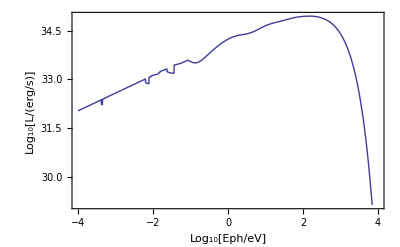

```mathematica
Plot[Log[10,L[10^(Eph)/erg2ev]],{Eph,Log[10,10^-4],Log[10,10^4]},Axes->False, Frame->True,FrameLabel->{"Log_10[Eph/eV]", "Log_10[L/(erg/s)]"}]
```

Bremsstrahlung

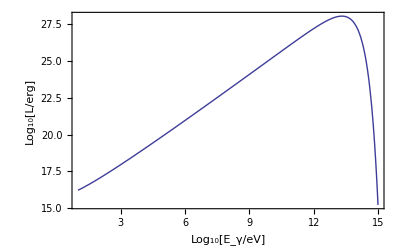

```mathematica
Bremsstrahlung
Plot[Log10[(10^Eγ)^2*V*fvol*NIntegrate[n*σ[Eγ,Ee]*I1[Ee],{Ee,10^Eγ,∞},MaxRecursion->15]*ev2erg],{Eγ,Log10[10^1],Log10[10^15]},Axes->False, Frame->True,FrameLabel->{"Log_10[E_γ/eV]", "Log_10[L/erg]"}]
```

Compton Inverse

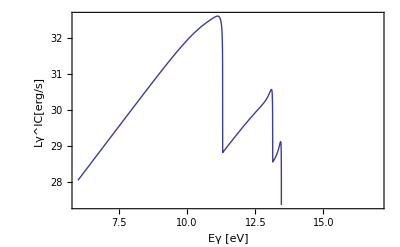

```mathematica
Inverse Compton
Plot[Log[10,luminosidadIC[10^Eγ]/erg2ev], {Eγ,-5.5,15}, PlotPoints->10,Frame->True,FrameLabel->{"Log Eγ [eV]","Log Lγ^IC[erg/s]"},Axes->False]
```

Proton^2

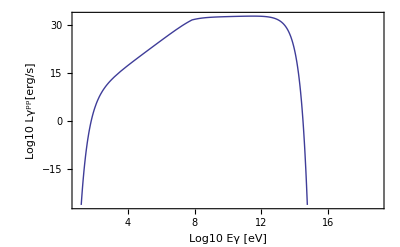

```mathematica
Proton Proton
Plot[Log[10,(10^Eγ)^2*fvol*V*(2*c *n)/κ *Ap*10^-27 NIntegrate[1/(√(Eπ^2-Eπrep^2))(Eprep + Eπ/κ)^-α*ⅇ^(-(Eprep + Eπ/κ)/Epmax)*(34.3 +1.88 *Log[(Eprep + Eπ/κ) *10^12]+0.25 *Log[(Eprep + Eπ/κ)* 10^12]^2) ,{Eπ,(10^Eγ)+Eπrep^2/(4 *(10^Eγ)),10^16},MaxRecursion->20]/erg2ev],{Eγ,Log10[10^1],Log10[10^19]},Frame->True,FrameLabel->{"Log10 Eγ [eV]","Log10 Lγ^pp[erg/s]"},Axes->False]
```

## Observaciones

```mathematica
radio:={{5.4*10^-6, 8.4*10^-14*f2L}, {8.6*10^-6, 1.1*10^-13*f2L}}
ex:={{5.4*10^2, 4.42*10^-10*f2L}, {1.6*10^3, 4.05*10^-10*f2L}, {3.4*10^3, 3.12*10^-10*f2L}, {6.3*10^3, 2.29*10^-10*f2L}, {8.6*10^3, 1.69*10^-10*f2L}, {1.4*10^4, 1.30*10^-10*f2L}, {2.2*10^4, 8.04*10^-11*f2L}, {2.9*10^4, 4.55*10^-11*f2L}}
gamlat:={{7.4*10^8, 5.4*10^-12*f2L}, {1.8*10^9, 4.5*10^-12*f2L}, {4.6*10^9, 6.6*10^-12*f2L}, {1.4*10^10, 1.0*10^-11*f2L}, {3.4*10^10, 2.1*10^-11*f2L}, {1.0*10^11, 1.9*10^-11*f2L}, {2.5*10^11, 1.8*10^-11*f2L}}
gamhess:={{2.9*10^11, 4.4*10^-11*f2L}, {3.4*10^11, 3.3*10^-11*f2L}, {7.4*10^11, 2.6*10^-11*f2L}, {1.4*10^12, 3.4*10^-11*f2L}, {4.6*10^12, 2.8*10^-11*f2L}, {5.4*10^12, 2.4*10^-11*f2L}, {6.3*10^12, 2.0*10^-11*f2L}, {8.6*10^12, 1.5*10^-11*f2L}, {1.8*10^13, 9.9*10^-12*f2L}, {3.4*10^13, 1.2*10^-11*f2L}, {4.0*10^13, 3.6*10^-12*f2L}, {8.6*10^13, 2.3*10^-12*f2L}}
8.4*10^-14*f2L
```

2.26141×10^33

```mathematica
Show[Plot[{Log[10,L[10^(Eγ)/erg2ev]],Log10[(10^Eγ)^2*V*fvol*NIntegrate[n*σ[Eγ,Ee]*I1[Ee],{Ee,10^Eγ,∞},MaxRecursion->15]*ev2erg],Log[10,(10^Eγ)^2*fvol*V*(2*c *n)/κ *Ap*10^-27 NIntegrate[1/(√(Eπ^2-Eπrep^2))(Eprep + Eπ/κ)^-α*ⅇ^(-(Eprep + Eπ/κ)/Epmax)*(34.3 +1.88 *Log[(Eprep + Eπ/κ) *10^12]+0.25 *Log[(Eprep + Eπ/κ)* 10^12]^2) ,{Eπ,(10^Eγ)+Eπrep^2/(4 *(10^Eγ)),10^16},MaxRecursion->20]/erg2ev],Log[10,luminosidadIC[10^Eγ]/erg2ev]},{Eγ,Log[10,10^-6],Log[10,10^15]},Axes->False, Frame->True,FrameLabel->{"Log_10[Eγ/eV]", "Log_10[L/(erg/s)]"}],ListPlot[{Log10[radio],Log10[ex],Log10[gamlat],Log10[gamhess]}],PlotRange->{{-6,16},{20,39}},PlotRangeClipping->True,Frame->True,GridLines->Automatic,GridLinesStyle->GrayLevel[.9],Axes->False]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

NIntegrate::inumr: The integrand 2.57703×10^47\ « 3 »\ (1 + 5.00989×10^-13\ (1 - 65344.8/(1 + Times[« 2 »])\ « 1 »\ Eph)/(1 - « 23 »/Ee)^2\ (1 + 1.00099×10^-6/Plus[« 2 »]\ Ee)\ Ee^2 - « 1 » + 65344.8/(1 - « 23 »/Ee)\ « 1 »\ Eph + 130690.\ Log[65344.8/(1 + Times[« 2 »])\ Ee^2\ Eph]/(1 - 1.00099×10^-6/Ee)\ Ee^2\ Eph)/(-1 + ⅇ^4301.63\ Eph)\ Ee^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 0.023247}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ee near {Ee} = {6.69621×10^6}. NIntegrate obtained 5.84868×10^20 and 1.65415×10^19 for the integral and error estimates.

$Aborted

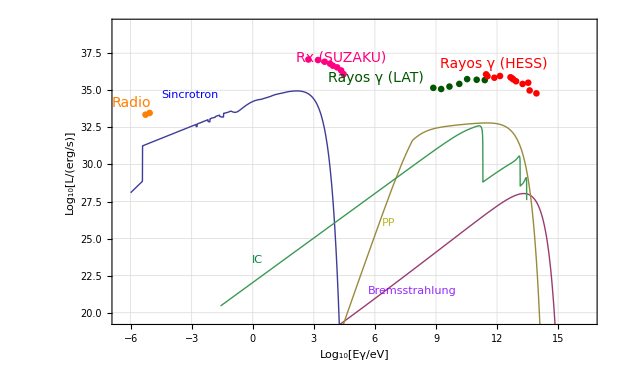

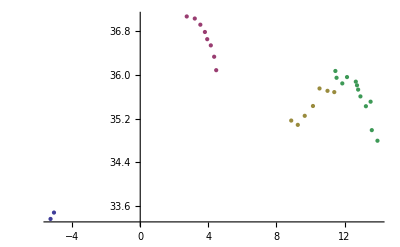

```mathematica
Show[ListPlot[{Log10[radio],Log10[ex],Log10[gamlat],Log10[gamhess]}]]
```